```mathematica
SetDirectory["/Users/yasamanyazdi/Desktop/W3d"];(*Directory should be set to where the causet2.wl package is saved*)
<<"causet2.wl";(*importing the package causet2.wl which has things like the sprinkling and causal/link matrices defined in it*)
```

### Sprinkling a 2+1D Diamond in Minkowski Spacetime

```mathematica
h= 1;(*Height of the diamond*)
NN=5000;(*NN is the number of elements. Strictly NN should be drawn from a Poisson distribution with this value as the mean*)
P=CSMinkowski3Diamond[h,NN]; (*Sprinkling the diamond*)
(*computing the causal and link matrices and converting them to floats, since that speeds up calculations, e.g. comparisons*)
c=CausalMatrix[P]//N;
L=LinkMatrix[P]//N;
rho=NN/CVolume[P];(*rho is the sprinkilng density*)
```

### Finding the Length of the Longest Chain between each pair of elements

```mathematica
maxlength=SparseArray[c]["NonzeroValues"];(*initializing the array of max chain lengths to be 1, when there is a causal relation between two elements*)
(*only keeping the nonzero entries in a 1d array, since only these entries can have a chain of any length between them.  also, this will speed up the code, since only a fraction of the entries will need to be compared*)

positions=SparseArray[c//Flatten]["NonzeroPositions"]//Flatten;(*storing the positions (in the flattened causal matrix) of the nonzero elements in a 1d array, so that at the end of the calculation the matrix of max chain lengths can be reconstructed*)

zeroCompare=Table[0,{i,1,NN},{j,1,NN}];(*matrix of zeros to compare the chains matrix to*)
```

```mathematica
counter=1;(*the length of chains in the current iteration. it starts out as a single link*)
chains=L;(*chains is the matrix (L^n)_xy. if entry xy is nonzero, it indicates that there is at least one chain of length n between elements x and y.  an additional advantage of working with the link matrix instead of the causal matrix is that its powers are sparser than powers of the causal matrix, meaning that there will be fewer nonzero entries to compare to the list of maximal chain lengths*)
Do[
counter++;

chains=chains.L;(*finding chains of length i+1 composed of links*)

If[chains==zeroCompare,Break[]];(*if chains = 0, we can stop the loop, since no longer chains will be found*)

length=Flatten[chains][[positions]];(*flattening the matrix to a 1d array and finding only the entries corresponding to the positions of nonzero causal matrix entries*)

comparePositions=SparseArray[length//Flatten]["NonzeroPositions"]//Flatten;(*finding the positions in the new array that are nonzero*)

length=SparseArray[length]["NonzeroValues"];(*keeping only the nonzero entries of the new array*)

length=counter*HeavisideTheta[length];(*currently the length array has the number of link chains between two points, but we want the length of the chain*)
(*since the chains are longer in each iteration of the loop, we can replace the corresponding entries in the max length array with the updated values *)
maxlength[[comparePositions]]=length
(*looping up to NN-1 (i.e. L^(NN-1)), since the longest possible chain in a causet of size NN has NN-1 links*)
,{i,1,NN-2}]
```

```mathematica
(*now that we have the maximal chain lengths, we can reconstruct the matrix M_xy of maximal chain lengths*)
```

```mathematica
flattenedProperTimes=Table[0,{i,1,NN*NN}];(*NN^2 array of zeros*)

Do[flattenedProperTimes[[ positions[[i]] ]]=maxlength[[i]],{i,1,Length[positions]}];(*replace entries with max chain lengths according to the position of nonzero causal matrix entries in flattened causal matrix*)

properTimes3=Table[flattenedProperTimes[[1+(i-1)*NN;;NN+(i-1)*NN]],{i,1,NN}];(*unflatten to a square NN x NN matrix*)
```

### Defining the SJ Wightman function

```mathematica
(*1.77<m3<2.62*)
m3=1.854;
```

```mathematica
GR=Table[If[c[[i,j]]==1,N[(Pi rho/12)^(1/3)m3/(2 Pi properTimes3[[i,j]])],0]
,{i,1,NN},{j,1,NN}];(*The retarded Green function in terms of the proper times (proportional to the length of the longest chain)*)
```

```mathematica
M=N[I](GR-Transpose[GR]);(*M is iΔ*)
```

```mathematica
{EE,VV}=Eigensystem[N[M]];(*EE and VV are the eigenvalues and eigenvectors of iΔ respectively*)
```

```mathematica
EE=Chop[EE];(*setting to 0 any eigenvalues that are smaller than 10^-10*)
W=Transpose[VV].DiagonalMatrix[Clip[N[EE],{0,Max[N[EE]]}]].Conjugate[VV];(*Constructing the SJ Wightman function out of the positive eigenvalues and eigenvectors of iΔ*)
```

### Defining an inner subdiamond

```mathematica
diamond=P[[1]];(*The diamond coordinates*)
```

```mathematica
innersize=0.2;
```

```mathematica
innerdiamondinds={};counter=0;
Do[
If[(diamond[[i,3]]≥0&&diamond[[i,3]]<innersize&&(diamond[[i,1]]^2+diamond[[i,2]]^2<(innersize-diamond[[i,3]])^2))
||
(diamond[[i,3]]<0&&diamond[[i,3]]>-innersize&&(diamond[[i,1]]^2+diamond[[i,2]]^2<(-innersize-diamond[[i,3]])^2)),
innerdiamondinds=Append[innerdiamondinds,i];counter++]
,{i,1,NN}]
```

### Computing proper times and proper distances according to the Minkowski Metric

```mathematica
time=diamond[[All,-1]];
space=diamond[[All, ;;-2]];

timepairs=Subsets[time,{2}];
spacepairs=Subsets[space,{2}];
timediffs=Apply[Subtract,timepairs,2];
spacediffs=Apply[Subtract,spacepairs,1];
timediffsquares=timediffs^2;
spacediffsquares=MapThread[Dot,{spacediffs,spacediffs},1];
fulldiffsquares=timediffsquares-spacediffsquares;
distSquare=Table[∞,{i,1,NN},{j,1,i}];
counter=1;
Do[distSquare[[i]]=Join[distSquare[[i]],fulldiffsquares[[counter;;(counter-1)+NN-i]]];
counter=counter+NN-i,{i,1,NN}]
```

```mathematica
Winner=W[[innerdiamondinds,innerdiamondinds]];(*Values of W for the inner diamond elements*)
distSquareinner=distSquare[[innerdiamondinds,innerdiamondinds]];(*Values of the proper time and distance for the inner diamond elements*)
```

```mathematica
MMinner=Length[innerdiamondinds];
```

#### Timelike pairs: Plotting Re[W] vs. τ when τ^2 > 0

```mathematica
timeWinner={};
Do[
If[distSquareinner[[i,j]]<∞&&distSquareinner[[i,j]]>0,timeWinner=Append[timeWinner,{Abs[√distSquareinner[[i,j]]],Re[Winner[[i,j]]]}]]
,{i,1,MMinner},{j,1,MMinner}]
```

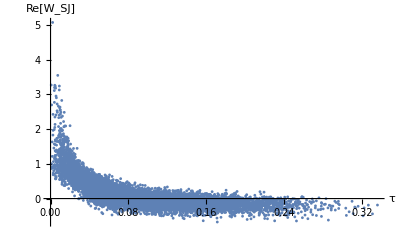

```mathematica
ListPlot[timeWinner,PlotStyle->{PointSize[0.005]},PlotRange->All,AxesLabel-> {"τ","Re[W_SJ]"}]
```

#### Spacelike pairs: Plotting Re[W] vs. |d| when d^2 < 0

```mathematica
spaceWinner={};
Do[
If[distSquareinner[[i,j]]<0,spaceWinner=Append[spaceWinner,{Abs[√distSquareinner[[i,j]]],Re[Winner[[i,j]]]}]]
,{i,1,MMinner},{j,1,MMinner}]
```

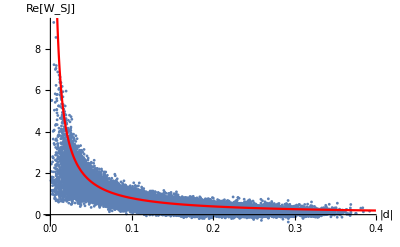

```mathematica
Show[{ListPlot[spaceWinner,PlotStyle->{PointSize[0.005]},PlotRange->All,AxesLabel-> {"|d|","Re[W_SJ]"}],Plot[1/( 4Pi τ),{τ,0,.4},PlotStyle->Red,PlotRange->All,PlotLegends->{"Re[W_Mink]"}]}]
```